```mathematica
h={{-g, -g},{-g, 2ξ-g}};
h//MatrixForm
```

(-g | -g
-g | -g+2 ξ)

```mathematica
Eigenvalues[h]
```

{-g+ξ-√(g^2+ξ^2),-g+ξ+√(g^2+ξ^2)}

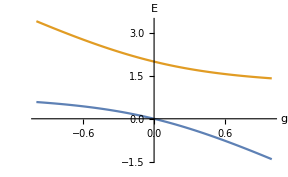

/Users/josh/Documents/Code/structure_work/project//images/sol2.pdf

```mathematica
h1plot=Plot[Evaluate@Eigenvalues[h/.ξ->1],{g,-1,1},
AxesLabel->{g,"E"},
ImageSize->4*72]
Export[NotebookDirectory[]<>"/images/sol2.pdf",h1plot]
```

```mathematica
h2=({{2-2g, -g, -g, -g, -g, 0}, {-g, 4-2g, -g, -g, 0, -g}, {-g, -g, 6-2g, 0, -g, -g}, {-g, -g, 0, 6-2g, -g, -g}, {-g, 0, -g, -g, 8-2g, -g}, {0, -g, -g, -g, -g, 10-2g}});
```

```mathematica
Eigenvalues[h2]
```

{-2 (-3+g),-2 (-3+g),Root[640-1248 g+432 g^2+(-624+784 g-144 g^2) #1+(196-144 g+12 g^2) #1^2+(-24+8 g) #1^3+#1^4&,1],Root[640-1248 g+432 g^2+(-624+784 g-144 g^2) #1+(196-144 g+12 g^2) #1^2+(-24+8 g) #1^3+#1^4&,2],Root[640-1248 g+432 g^2+(-624+784 g-144 g^2) #1+(196-144 g+12 g^2) #1^2+(-24+8 g) #1^3+#1^4&,3],Root[640-1248 g+432 g^2+(-624+784 g-144 g^2) #1+(196-144 g+12 g^2) #1^2+(-24+8 g) #1^3+#1^4&,4]}

```mathematica
Eigenvalues[h2/.{g->0}]
```

{10,8,6,6,4,2}

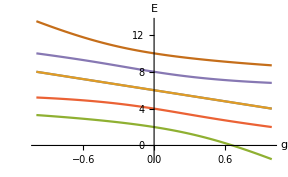

/Users/josh/Documents/Code/structure_work/project//images/sol4.pdf

```mathematica
h2plot=Plot[Evaluate@Eigenvalues[h2],{g,-1,1},
AxesLabel->{g,"E"},
ImageSize->4*72]
Export[NotebookDirectory[]<>"/images/sol4.pdf",h2plot]
```

```mathematica
N@Eigenvalues[h2/.g->0]
```

{10.,8.,6.,6.,4.,2.}